```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
<<RLBot`
SetDirectory[NotebookDirectory[]];
```

```mathematica
data = ImportNDJSON["aerial_turn_no_damping.ndjson",{1}];
```

```mathematica
ListLinePlot[Transpose[#["w"]& /@ data], PlotRange->All]
```

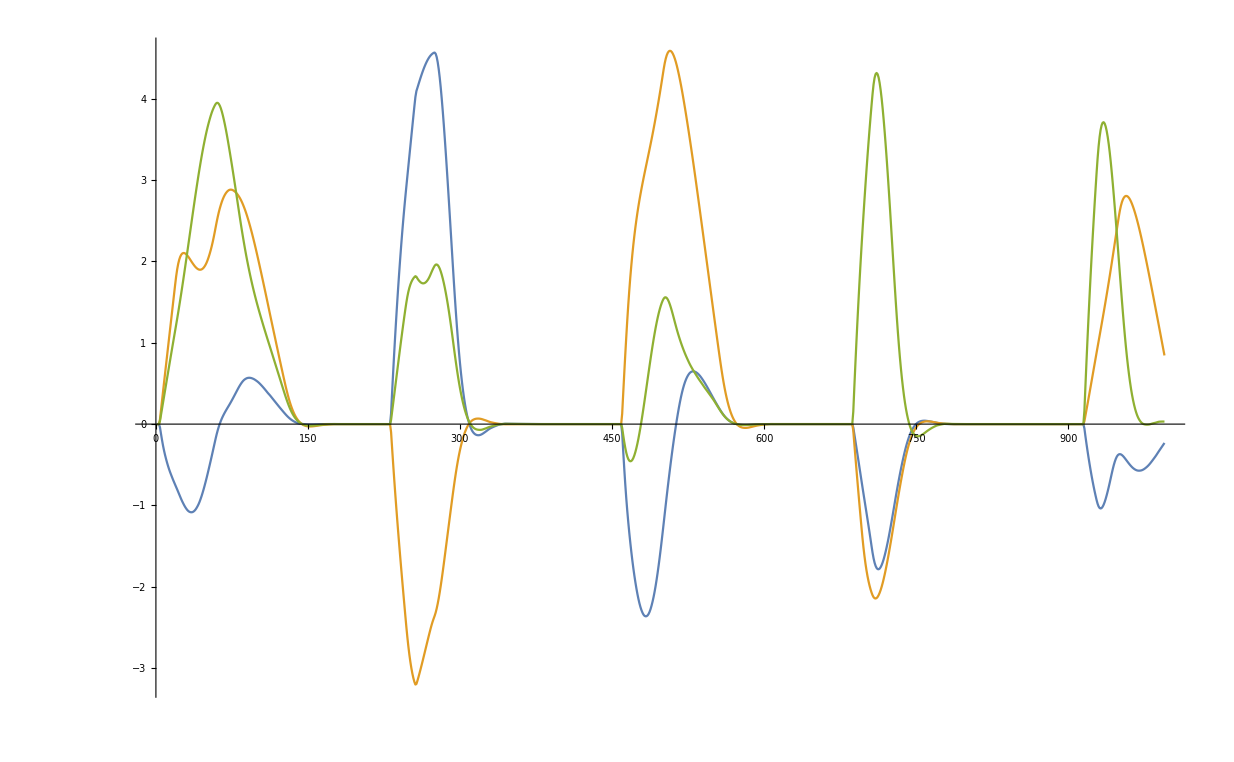

-Graphics-

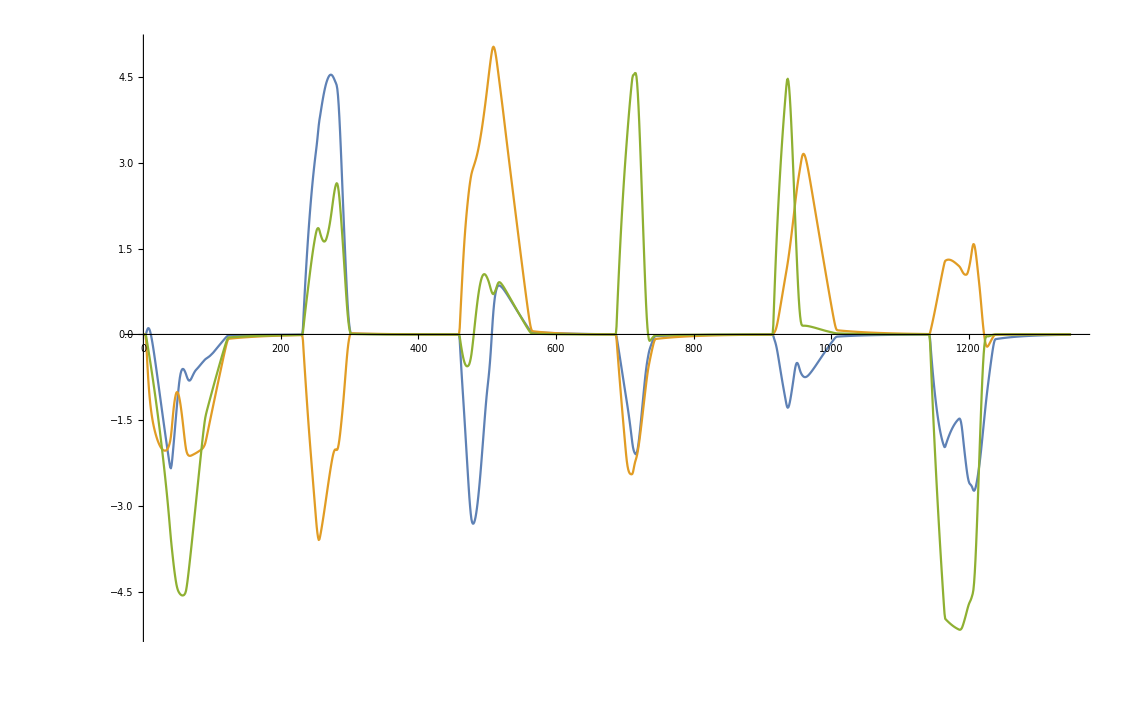

-Graphics-